# Random Markov Walkers

## Functions

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sanchez.hmsc/Documents/GitHub/MoNeT/Dev/HectorSanchez/GeographicalLayoutsGenerator

## Pointset

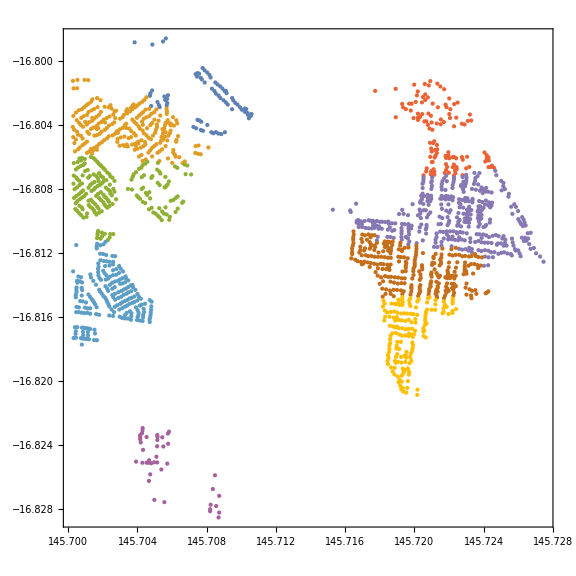

```mathematica
coordinates=Import["./YorkeysKnob/YorkeysKnob_Coordinates.csv"];
clustered=FindClusters[coordinates,Method->"NeighborhoodContraction"];
listPlot=ListPlot[clustered,
AspectRatio->1,
Frame->True,
FrameStyle->Thick,
Axes->None,
PlotStyle->PointSize[Small],
ImageSize->Large
]
```

## Kernel

```mathematica
kernel=Import["./YorkeysKnob/YorkeysKnob_Kernel.csv"][[2;;All]];
```

```mathematica
startingPoint=1;
initialState=ConstantArray[0,kernel//Length]//ReplacePart[#,startingPoint->1]&;
markov=DiscreteMarkovProcess[initialState,kernel];
(**)
data=RandomFunction[markov,{0,1000}];
tally=(data//Normal)[[All,All,2]][[1]]//Tally//Sort;
barChartFrequency=BarChart[tally[[All,2]],
ChartStyle->"LakeColors",
ChartLabels->tally[[All,1]],
ImageSize->Large,
Frame->True,
FrameStyle->Thick,
FrameTicksStyle->Directive[8],
FrameLabel->(Style[#,25]&/@{"Node ID","Visit Frequency"})
];
```

```mathematica
initialState=Table[ConstantArray[0,kernel//Length]//ReplacePart[#,i->1]&,{i,{1,10,19,28,37}}];
markov=DiscreteMarkovProcess[#,kernel]&/@initialState;
data=RandomFunction[#,{0,5000}]&/@markov;
ListPlot[data,
Filling->None,
PlotRange->{All,{1,kernel//Length}},
Frame->True,
FrameStyle->Thick,
ImageSize->1000,
GridLines->{Range[0,100000,100],Range[1,50,9]},
GridLinesStyle->Directive[Gray,Opacity[.2]],
FrameLabel->(Style[#,20]&/@{"Day","Node"}),
(*AspectRatio->1,*)
PlotStyle->Directive[Opacity[.5],PointSize[Medium]],
ImageSize->Large
]
```